```mathematica
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
```

```mathematica
s=NDSolve[{y''[x]==y[x]*((-2/(x))*Exp[-0*x]-2*(-0.5)),y[0.00005]==0,y'[0.00005]==1 },y,{x,0.00005,300}]
```

{{y→InterpolatingFunction[{{0.00005, 300.}}, <>]}}

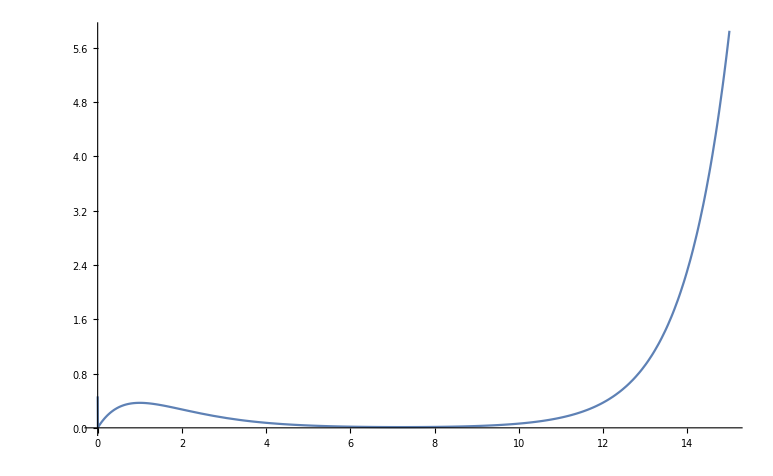

```mathematica
Plot[Evaluate[y[x]/.s],{x,0,15},PlotRange->All]
```

```mathematica
y[7.5]/.s
```

{0.011212}

```mathematica
ClassicalRungeKuttaCoefficients[4,prec_]:=With[{amat={{1/2},{0,1/2},{0,0,1}},bvec={1/6,1/3,1/3,1/6},cvec={1/2,1/2,1}},N[{amat,bvec,cvec},prec]]
```

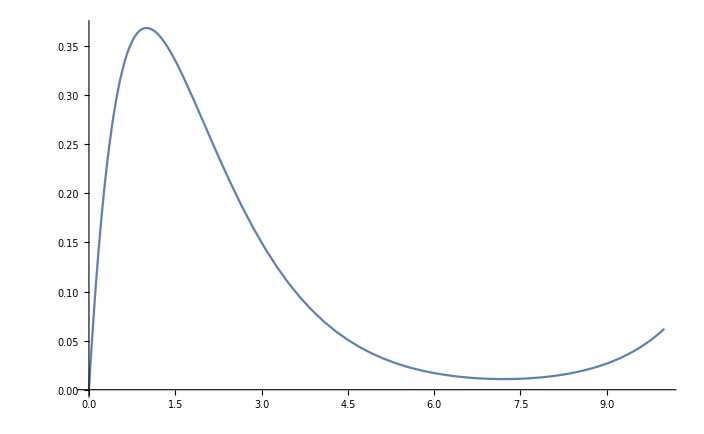

```mathematica
sol = NDSolve[{y''[x]==y[x]*((-2/(x))*Exp[-0*x]-2*(-0.5)),y[0.00005]==0,y'[0.00005]==1 },y,{x,0.00005,300},Method->{"ExplicitRungeKutta","DifferenceOrder"->4,"Coefficients"->ClassicalRungeKuttaCoefficients},StartingStepSize->5/10000];
Plot[y[t]/.sol,{t,0,10}]
```